# Regression

## Linear regression

### Model fitting

Imagine we have some data taken from an experiment and we would like to find a model that fits the data well.

Here is some data I took earlier. Can you figure out a good model for this data? Once you have a good idea for a model, try using Mathematica’s FindFit function to test it with the data. How would you verify that your model is a good fit for the data?

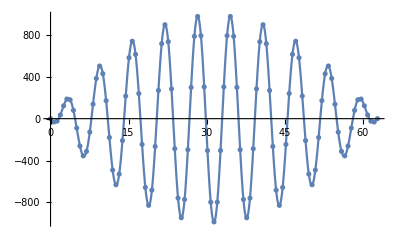

```mathematica
data=;
data;
Show[{ListPlot[data],Plot[(x^2-20 π x)Cos[x],{x,0,20 π}]}]
```

#### Analysis

Here is how I created that mystery data:

```mathematica
data = Table[{x,(x^2-20 π x) Cos[x]},{x,0,20 π, 20π/100}];
Iconize[data,"Mystery data"]
```

The first thing we should do is try to plot the data to see if we can recognise anything

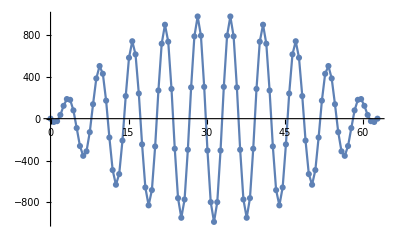

```mathematica
ListLinePlot[data,PlotMarkers->Automatic]
```

If we have a good idea for a model that might fit the data, then we can use FindFit to look for the parameters that best fit the data. This looks like the plot of cos(x) modulated by a quadratic so let’s try to fit a linear model of that form to the data:

```mathematica
model=(a1+a2 x+a3 x^2) Cos[x]/.FindFit[data,(a1+a2 x+a3 x^2) Cos[x],{a1,a2,a3},x]
```

(5.88143×10^-13-62.8319 x+1. x^2) Cos[x]

Now we plot the model against the data

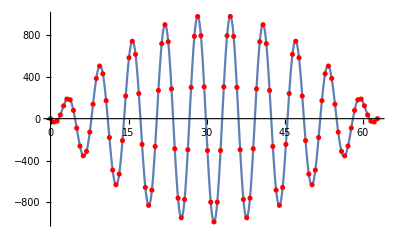

```mathematica
Show[Plot[model,{x,0,20 π}],ListPlot[data,PlotStyle->Red]]
```

Now that we have seen a simple example, let’s apply what we have learned in the lectures to see if we can reproduce this and in the process understand what Mathematica has done to find a good fit to the data.

### Linear Regression for a linear function

We will start with a simple problem: find the line that best fits some data by determining the best fit parameters (α, β) in our model f(x)=α+β x.

The first thing we need is to collect some data samples. Normally, this could come from some experimental measurements, but for this example we will just generate some data ourselves.  In the real world we will never have perfectly clean measurements so we will expect some random noise in our samples. To simulate this, we will add some random noise when we’re generating the data we want to fit.

```mathematica
data=Table[{x,3+2 x+RandomVariate[NormalDistribution[0,0.3]]},{x,0,5,0.5}];
MatrixForm[data]
Length[data]
```

(0. | 2.84653
0.5 | 4.01135
1. | 5.28594
1.5 | 5.43961
2. | 7.38134
2.5 | 7.53445
3. | 9.06041
3.5 | 10.3623
4. | 10.8398
4.5 | 11.8081
5. | 13.1462)

11

Now the first column are the values of x_i and the second column is f(x_i). Let’s extract those two columns from the matrix.

```mathematica
xi=data[[All,1]];
fxi=data[[All,2]];
```

The next thing we need to do is build up the matrix A representing our model evaluated for each value of x_i

```mathematica
A=Table[{1,x},{x,xi}];
MatrixForm[A]
```

(1 | 0.
1 | 0.5
1 | 1.
1 | 1.5
1 | 2.
1 | 2.5
1 | 3.
1 | 3.5
1 | 4.
1 | 4.5
1 | 5.)

```mathematica
MatrixForm[{α,β}]
```

(α
β)

```mathematica
A
```

{{1,0.},{1,0.5},{1,1.},{1,1.5},{1,2.},{1,2.5},{1,3.},{1,3.5},{1,4.},{1,4.5},{1,5.}}

```mathematica
AT=Transpose[A]
```

{{1,1,1,1,1,1,1,1,1,1,1},{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}}

Our model is then A(α
β)=f(x_i). The matrix A is an example where we have many rows but only two columns, so this is an over-constrained problem. As such we won’t be able to find a perfect solution (f(x_i) is not in the column space of A!), so we will look for a solutions that minimises ||A(α
β)=f(x_i)||. We saw how to do this in our linear algebra examples, where we had three ways to find the best fit solution:

#### Method 1: Directly minimise ||A(α β)=f(x_i)||

We can numerically search for the minimum over the parameters α and β. This is an example of an unconstrained convex optimisation problem

```mathematica
{min,sol}=FindMinimum[Norm[A.{α,β}-fxi]^2,{α,β}]
```

{0.986194,{α→2.93457,β→2.01585}}

We now check visually that we have indeed found the minimum:

```mathematica
Show[Plot3D[Norm[A.{α,β}-fxi]^2,{α,1,5},{β,1,3}],Graphics3D[Point[{3.23,1.93,Norm[A.{3.23,1.93}-fxi]^2}]]]
```

-Graphics3D-

This is equivalent to solving A^T A x̂=A^T f(x_i), i.e. using using A^Tto project onto the column space of A . Note that (A^T A)^-1 exists when A has independent columns [N(A) = N(A^T A)].

```mathematica
MatrixForm[Transpose[A].A].MatrixForm[{α,β}]==MatrixForm[Transpose[A].fxi]
```

(11. | 27.5
27.5 | 96.25).(α
β)==(87.7161
274.726)

```mathematica
LinearSolve[Transpose[A].A,Transpose[A].fxi]
```

{2.93457,2.01585}

```mathematica
Inverse[Transpose[A].A].Transpose[A].fxi
```

{2.93457,2.01585}

```mathematica
LeastSquares[A,fxi]
```

{2.93457,2.01585}

#### Method 2: QR

Recall that we saw that we could solve A^T A x̂=A^T f(x_i) efficiently if we had the QR decomposition of A. We have A^T A=(Q R)^T(QR) = R^T Q^T Q R=R^T R and A^T f(x_i)=(Q R)^T f(x_i)=R^T Q^T f(x_i) so our problem reduces to R x̂=Q^T b.

```mathematica
{Q,R}=QRDecomposition[A];
```

```mathematica
MatrixForm[R].MatrixForm[{α,β}]==MatrixForm[Q.fxi]
```

(-3.31662 | -8.29156
0. | 5.24404).(α
β)==(-26.4474
10.5712)

```mathematica
LinearSolve[R,Q.fxi]
```

{2.93457,2.01585}

```mathematica
Inverse[R].Q.fxi
```

{2.93457,2.01585}

#### Method 3: Pseudoinverse

Our third approach is to use the pseudoinverse to solve the problem directly.

```mathematica
PseudoInverse[A].fxi
```

{2.93457,2.01585}

We could also this using the singular value decomposition

```mathematica
{U,Σ,V}=SingularValueDecomposition[A];
```

```mathematica
ΣPlus=PseudoInverse[Σ];
ΣPlus//MatrixForm
```

(0.0978929 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.587335 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
V.ΣPlus.Transpose[U].fxi
```

{2.93457,2.01585}

### Overfitting and under-fitting

```mathematica
"With four parameters I can fit an elephant, and with five I can make him wiggle his trunk."
```

With four parameters I can fit an elephant, and with five I can make him wiggle his trunk.

We might think that we could obtain a better fit by introducing more parameters into our model. Similarly we might think that we could save some time by using fewer parameters. While this might be true in some cases, in many cases  it leads to problems of overfitting and under-fitting, respectively. Let’s use Mathematica’s Fit to fit three models to the data, one with too few parameters, one with two many, and one with the correct number

```mathematica
fit0=Fit[data,{1},{x}];
fit1=Fit[data,{1,x},{x}];
fit10=Fit[data,Table[x^i,{i,0,10}],{x}];
```

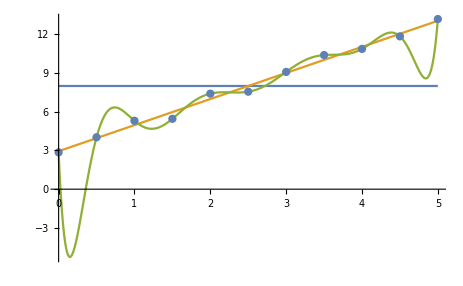

```mathematica
Show[Plot[{fit0,fit1,fit10},{x,0,5}],ListPlot[data]]
```

The green curve representing a 10th order polynomial certainly fits the blue points better (it exactly passes through them all - interpolation!) but it is clearly a worse fit than the orange. We have overfit our model. We could check for this by adding another point (which was not used in the training) and checking if it fits the model.

Similarly, the blue line (0th order polynomial) is an underfit and is not a good model for the data.

### Linear Regression for a nonlinear function (but still linear in parameters)

There is nothing in linear regression that assumes our model must be a liner function of the variables. Let’s try it with a nonlinear function

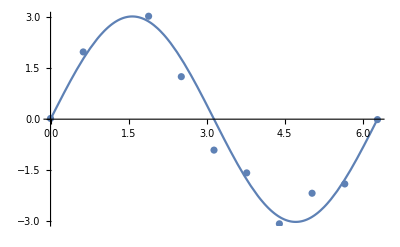

```mathematica
dataSin=Table[{x,3Sin [x]+RandomVariate[NormalDistribution[0,0.3]]},{x,0,2 π,2 π/10}];
fitSin=Fit[dataSin,{Sin[x]},{x}];
Show[Plot[fitSin,{x,0,2 π}],ListPlot[dataSin]]
```

### Linear Regression in multiple dimensions

It is straightforward to generalise to data in multiple dimensions:

```mathematica
data2D=Flatten[Table[{x,y,x^2+y^2+RandomVariate[NormalDistribution[0,0.5]]},{x,-5,5},{y,-5,5}],1];
```

```mathematica
fit2D=Fit[data2D,{1,x,y,x^2,y^2,x y},{x,y}];
```

```mathematica
Show[Plot3D[fit2D,{x,-5,5},{y,-5,5}],ListPointPlot3D[data2D]]
```

-Graphics3D-

```mathematica
xi=data2D⟦All,1⟧;
yi=data2D⟦All,2⟧;
fxi=data2D⟦All,3⟧;
A=Transpose[{ConstantArray[1,Length[xi]],xi,yi,xi^2,xi yi,yi^2}];
MatrixForm[A]
```

(1 | -5 | -5 | 25 | 25 | 25
1 | -5 | -4 | 25 | 20 | 16
1 | -5 | -3 | 25 | 15 | 9
1 | -5 | -2 | 25 | 10 | 4
1 | -5 | -1 | 25 | 5 | 1
1 | -5 | 0 | 25 | 0 | 0
1 | -5 | 1 | 25 | -5 | 1
1 | -5 | 2 | 25 | -10 | 4
1 | -5 | 3 | 25 | -15 | 9
1 | -5 | 4 | 25 | -20 | 16
1 | -5 | 5 | 25 | -25 | 25
1 | -4 | -5 | 16 | 20 | 25
1 | -4 | -4 | 16 | 16 | 16
1 | -4 | -3 | 16 | 12 | 9
1 | -4 | -2 | 16 | 8 | 4
1 | -4 | -1 | 16 | 4 | 1
1 | -4 | 0 | 16 | 0 | 0
1 | -4 | 1 | 16 | -4 | 1
1 | -4 | 2 | 16 | -8 | 4
1 | -4 | 3 | 16 | -12 | 9
1 | -4 | 4 | 16 | -16 | 16
1 | -4 | 5 | 16 | -20 | 25
1 | -3 | -5 | 9 | 15 | 25
1 | -3 | -4 | 9 | 12 | 16
1 | -3 | -3 | 9 | 9 | 9
1 | -3 | -2 | 9 | 6 | 4
1 | -3 | -1 | 9 | 3 | 1
1 | -3 | 0 | 9 | 0 | 0
1 | -3 | 1 | 9 | -3 | 1
1 | -3 | 2 | 9 | -6 | 4
1 | -3 | 3 | 9 | -9 | 9
1 | -3 | 4 | 9 | -12 | 16
1 | -3 | 5 | 9 | -15 | 25
1 | -2 | -5 | 4 | 10 | 25
1 | -2 | -4 | 4 | 8 | 16
1 | -2 | -3 | 4 | 6 | 9
1 | -2 | -2 | 4 | 4 | 4
1 | -2 | -1 | 4 | 2 | 1
1 | -2 | 0 | 4 | 0 | 0
1 | -2 | 1 | 4 | -2 | 1
1 | -2 | 2 | 4 | -4 | 4
1 | -2 | 3 | 4 | -6 | 9
1 | -2 | 4 | 4 | -8 | 16
1 | -2 | 5 | 4 | -10 | 25
1 | -1 | -5 | 1 | 5 | 25
1 | -1 | -4 | 1 | 4 | 16
1 | -1 | -3 | 1 | 3 | 9
1 | -1 | -2 | 1 | 2 | 4
1 | -1 | -1 | 1 | 1 | 1
1 | -1 | 0 | 1 | 0 | 0
1 | -1 | 1 | 1 | -1 | 1
1 | -1 | 2 | 1 | -2 | 4
1 | -1 | 3 | 1 | -3 | 9
1 | -1 | 4 | 1 | -4 | 16
1 | -1 | 5 | 1 | -5 | 25
1 | 0 | -5 | 0 | 0 | 25
1 | 0 | -4 | 0 | 0 | 16
1 | 0 | -3 | 0 | 0 | 9
1 | 0 | -2 | 0 | 0 | 4
1 | 0 | -1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 2 | 0 | 0 | 4
1 | 0 | 3 | 0 | 0 | 9
1 | 0 | 4 | 0 | 0 | 16
1 | 0 | 5 | 0 | 0 | 25
1 | 1 | -5 | 1 | -5 | 25
1 | 1 | -4 | 1 | -4 | 16
1 | 1 | -3 | 1 | -3 | 9
1 | 1 | -2 | 1 | -2 | 4
1 | 1 | -1 | 1 | -1 | 1
1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 2 | 1 | 2 | 4
1 | 1 | 3 | 1 | 3 | 9
1 | 1 | 4 | 1 | 4 | 16
1 | 1 | 5 | 1 | 5 | 25
1 | 2 | -5 | 4 | -10 | 25
1 | 2 | -4 | 4 | -8 | 16
1 | 2 | -3 | 4 | -6 | 9
1 | 2 | -2 | 4 | -4 | 4
1 | 2 | -1 | 4 | -2 | 1
1 | 2 | 0 | 4 | 0 | 0
1 | 2 | 1 | 4 | 2 | 1
1 | 2 | 2 | 4 | 4 | 4
1 | 2 | 3 | 4 | 6 | 9
1 | 2 | 4 | 4 | 8 | 16
1 | 2 | 5 | 4 | 10 | 25
1 | 3 | -5 | 9 | -15 | 25
1 | 3 | -4 | 9 | -12 | 16
1 | 3 | -3 | 9 | -9 | 9
1 | 3 | -2 | 9 | -6 | 4
1 | 3 | -1 | 9 | -3 | 1
1 | 3 | 0 | 9 | 0 | 0
1 | 3 | 1 | 9 | 3 | 1
1 | 3 | 2 | 9 | 6 | 4
1 | 3 | 3 | 9 | 9 | 9
1 | 3 | 4 | 9 | 12 | 16
1 | 3 | 5 | 9 | 15 | 25
1 | 4 | -5 | 16 | -20 | 25
1 | 4 | -4 | 16 | -16 | 16
1 | 4 | -3 | 16 | -12 | 9
1 | 4 | -2 | 16 | -8 | 4
1 | 4 | -1 | 16 | -4 | 1
1 | 4 | 0 | 16 | 0 | 0
1 | 4 | 1 | 16 | 4 | 1
1 | 4 | 2 | 16 | 8 | 4
1 | 4 | 3 | 16 | 12 | 9
1 | 4 | 4 | 16 | 16 | 16
1 | 4 | 5 | 16 | 20 | 25
1 | 5 | -5 | 25 | -25 | 25
1 | 5 | -4 | 25 | -20 | 16
1 | 5 | -3 | 25 | -15 | 9
1 | 5 | -2 | 25 | -10 | 4
1 | 5 | -1 | 25 | -5 | 1
1 | 5 | 0 | 25 | 0 | 0
1 | 5 | 1 | 25 | 5 | 1
1 | 5 | 2 | 25 | 10 | 4
1 | 5 | 3 | 25 | 15 | 9
1 | 5 | 4 | 25 | 20 | 16
1 | 5 | 5 | 25 | 25 | 25)

```mathematica
PseudoInverse[A].fxi
```

{-0.000867845,0.0318724,-0.00152885,0.993604,0.00569326,1.01133}

```mathematica
fit2D
```

-0.000867845+0.0318724 x+0.993604 x^2-0.00152885 y+0.00569326 x y+1.01133 y^2

## Nonlinear regression

We haven’t covered it in the lectures, but we can also fit a non-linear model, where we have a non-linear function of the parameters. To start, let’s make up some data to use:

```mathematica
data=Table[Sqrt[x] Cos[x]+RandomReal[0.1{-1,1}],{x,100}];
```

We can fit a nonlinear model to this data

```mathematica
model=a1 x^a2 Cos[a3 x];
```

```mathematica
FindFit[data,model,{a1,a2,a3},x]
```

{a1→0.977425,a2→0.505404,a3→1.00001}

```mathematica
NonlinearModelFit[data,a1 x^a2 Cos[a3 x],{a1,a2,a3},x]
```

FittedModel[0.977425 x^0.505404 Cos[1.00001 x]]

Now we plot the model against the data to check it does fit

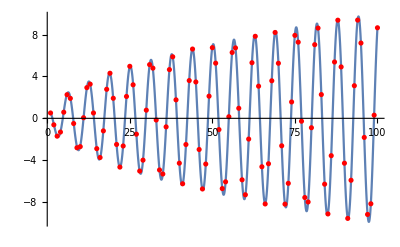

```mathematica
Show[Plot[Evaluate[model/.FindFit[data,model,{a1,a2,a3},x],{x,1,100}]],ListPlot[data,PlotStyle->Red]]
```

## Logistic regression

Finally, let’s look at an example of Logistic Regression. We will return to the MNIST Digits dataset we studied using Principal Component Analysis.

```mathematica
MNIST=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
```

```mathematica
MNISTtest=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
MNISTbynumber=GroupBy[MNIST,Last->First];
```

To save time, we will train the model using a subset of the data.

```mathematica
trainingset=RandomSample[MNIST,100];
```

We could use LogitModelFit to fit a model and then used that to build a function that takes in an image and returns a number, but rather than worrying about the messy details we can use Classify with the LogisticRegression method specified. This takes care of converting the image to a matrix and all the other messy details.

```mathematica
logistic=Classify[trainingset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[logistic]
```

Classifier information
Data type | Image
Number of classes | 10
Accuracy | (58.16.) %
Method | LogisticRegression
Single evaluation time | 7.02 ms/example
Batch evaluation speed | 5.68 examples/ms
Loss | 1.25 ± 0.3
Model memory | 838. kB
Training examples used | 100 examples
Training time | 2.41 s
 |

We can now treat this as a function that takes in an image and returns a number. Let’s look at some information about the function:

Let’s see how well it performs by testing it on a random sample of the test data

```mathematica
test=RandomSample[MNISTtest,1]
```

{-Graphics-→2}

```mathematica
logistic[-Graphics-]
```

9

```mathematica
Tally[Map[logistic[#⟦1⟧]==#⟦2⟧&,RandomSample[MNISTtest,1000]]]
```

{{False,364},{True,636}}

It’s right about 2/3 of the time. We could improve this by going back to the training step and using more training samples:

```mathematica
trainingset=RandomSample[MNIST,1000];
```

```mathematica
betterlogistic=Classify[trainingset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[betterlogistic]
```

Classifier information
Data type | Image
Number of classes | 10
Accuracy | (87.53.4) %
Method | LogisticRegression
Single evaluation time | 4.66 ms/example
Batch evaluation speed | 8. examples/ms
Loss | 0.466 ± 0.12
Model memory | 181. kB
Training examples used | 1000 examples
Training time | 5.59 s
 |

```mathematica
Tally[Map[betterlogistic[#⟦1⟧]==#⟦2⟧&,RandomSample[MNISTtest,1000]]]
```

{{True,855},{False,145}}

Now this is close to 90% accurate